```mathematica
GraphicsGrid[
 Map[MandelbrotSetPlot[#1, ColorFunction -> "SunsetColors", 
    Frame -> False] &, {{{0.2102 + 0.464 I, 0.4443 + 0.7062 I}, 
    Apply[Complex, {{0.2274, 0.5529}, {0.2455, 
       0.5717}}, {1}]}, {{}, {-0.743 + 0.175 I, -0.723 + 
      0.195 I}}}, {2}], ImageSize -> 600, Frame -> All, 
 FrameStyle -> Gray]
```

-Graphics-

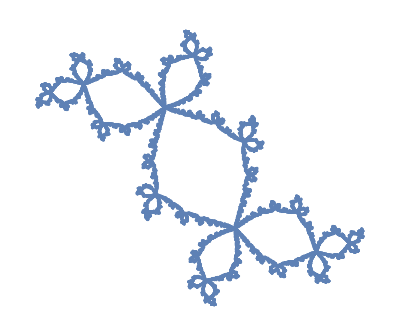

```mathematica
julia = JuliaSetPlot[z^2 + (-0.123 + 0.745 I), z, 
  PlotStyle -> AbsolutePointSize[1.6], ColorFunction -> None, 
  Frame -> False, Axes -> False]
```

```mathematica
m=MandelbrotSetPlot[]
```

-Graphics-

```mathematica
Export["Mandelbrot_set.png",m, ImageResolution->1000]
```

Mandelbrot_set.png